## Valon and parton distribution in P+A collision

```mathematica
SetDirectory[SystemDialogInput["Directory"]]
```

C:\Users\86177\Desktop\innovation\valon model

```mathematica
ExpandFileName["C:\\Users\\86177\\Desktop\\innovation\\valon model"]
```

C:\Users\86177\Desktop\innovation\valon model

```mathematica
<<PDFs`
```

```mathematica
Clear[g]
$Assumptions=y1∈Reals&&y2∈Reals&&y3∈Reals;
∫_0^1 (∫_0^(1-y1) (∫_0^(1-y1-y2) GUUD[y1,y2,y3]ⅆy3)ⅆy2)ⅆy1
```

1.

```mathematica
Solve[0.001281769756386444 g==1,g]
```

{{g→780.171}}

```mathematica
GUUD[y1_,y2_,y3_]:=g(y1 y2)^α y3^β DiracDelta[y1+y2+y3-1];
g=780.1713178341738;
GU[y_]:=g Beta[α+1,β+1]y^α (1-y)^(α+β+1);
GD[y_]:=g Beta[α+1,α+1]y^β (1-y)^(2α+1);
(*Q^2=100*)
Kall[z_]:=KNS[z]+L[z];
KNS[z_]:=0.333 z^0.45(1-z)^2.1 (1+5.0 z^0.5);
L[z_]:=1.881 z^0.133(1-z)^3.384 (1-0.991 z^0.31);
α=1.75;β=1.05;
xu[x_]:=NIntegrate[(2 GU[y]Kall[x/y]+GD[y]L[x/y]),{y,x,1}];
xd[x_]:=NIntegrate[( GD[y]Kall[x/y]+2GU[y]L[x/y]),{y,x,1}];
```

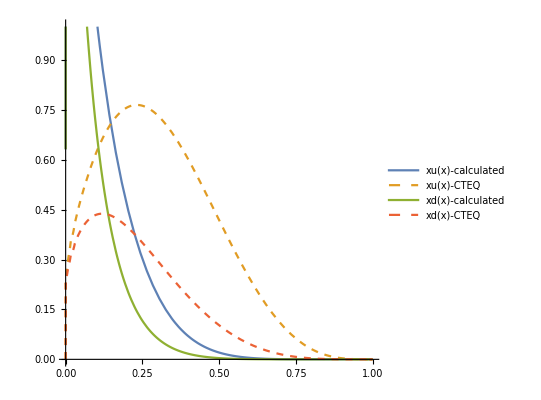

```mathematica
Plot[{xu[x],x PDFparton["u",x,1],xd[x],x PDFparton["d",x,1]},{x,0,1},PlotLegends->{"xu(x)-calculated","xu(x)-CTEQ","xd(x)-calculated","xd(x)-CTEQ"},AspectRatio->1,PlotRange->{0,1},PlotStyle->{Line,Dashed,Line,Dashed}]
```

## Net proton distribution in P+A collision

```mathematica
(*
OverTilde[Subscript[H, p-p']][n_]:=OverTilde[Subscript[H, p']][n]-OverTilde[Subscript[H, pbar']][n];OverTilde[Subscript[H, n-n']][n_]:=OverTilde[Subscript[H, neu']][n]-OverTilde[Subscript[H, nbar']][n];  
Hpp1m[n_]:=Hp1m[n]-Hpbar1m[n];Hnn1m[n_]:=Hn1m[n]-Hnbar1m[n];*)
```

```mathematica
(*∫_0^1 (∫_0^(1-y1) (∫_0^(1-y1-y2) y1^(n1-1)y2^(n2-1)y3^(n3-1)GUUD[y1,y2,y3]ⅆy3)ⅆy2)ⅆy1*)
GUUDm[n1_,n2_,n3_]:=(780.17132 Gamma[1.75+n1] Gamma[1.75+n2] Gamma[1.05+n3])/Gamma[4.55+n1+n2+n3];
GUUD1m[n1_,n2_,n3_]:=1/3^v Sum[(v!)/(v1!v2!(v-v1-v2)!)GUUDm[n1,n2,n3]Dm[n1,v1]Dm[n2,v2]Dm[n3,v-v1-v2],{v1,0,v},{v2,0,v-v1}];
GUU1m[m1_,m2_]:=GUUD1m[m1,m2,1];
GUD1m[m1_,m2_]:=GUUD1m[m1,1,m2];
```

```mathematica
N0=g^2 Beta[2α+2,2α+2β+4]Beta[2α+2,2β+2];
NewInt[func_,internal_]:=With[{F=Integrate[func,internal]},If[TrueQ[Head[F]==ConditionalExpression],F[[1]],F]]
Rp[x1_,x2_,x3_,x_]:=x1 x2 x3 GUUD[x1/x,x2/x,x3/x]/x^3;
Kallm[ni_]:=(0.73181 Gamma[-0.55+ni])/Gamma[2.55+ni]+(3.659 Gamma[-0.05+ni])/Gamma[3.05+ni]+(18.6551223 Gamma[-0.867+ni])/Gamma[3.517+ni]-(18.4872 Gamma[-0.557+ni])/Gamma[3.827+ni];     (*NewInt[Kall[z] z^(ni-2),{z,0,1}]*)
Lm[ni_]:=(18.6551223 Gamma[-0.867+ni])/Gamma[3.517+ni]-(18.4872 Gamma[-0.557+ni])/Gamma[3.827+ni]  (*NewInt[L[z] z^(ni-2),{z,0,1}]*);

(*sometimes always produce complex number owing to Hypergeometric2F1*)
Kallm[nj_,nk_]:=Gamma[1+nk] ((1.881 Gamma[-0.867+nj] Re@Hypergeometric2F1[-2.384,-0.867+nj,0.133+nj+nk,1])/Gamma[0.133+nj+nk]-(1.86407 Gamma[-0.557+nj] Re@Hypergeometric2F1[-2.384,-0.557+nj,0.443+nj+nk,1])/Gamma[0.443+nj+nk]+((0.333) Gamma[-0.55+nj] Re@Hypergeometric2F1[-1.1,-0.55+nj,0.45+nj+nk,1])/Gamma[0.45+nj+nk]+(1.665 Gamma[-0.05+nj] Re@Hypergeometric2F1[-1.1,-0.05+nj,0.95+nj+nk,1])/Gamma[0.95+nj+nk]);(*NewInt[z^(nj-2)(1-z)^(nk-1)Kall[z],{z,0,1}]*)


Lm[nj_,nk_]:=1.881 Gamma[3.384+nk] (Gamma[-0.867+nj]/Gamma[2.517+nj+nk]-(0.991 Gamma[-0.557+nj])/Gamma[2.827+nj+nk]) (*NewInt[z^(nj-2)(1-z)^(nk-1)L[z],{z,0,1}]*);
(*q=0.37; *)(*free parameter*)
qvi[vi_]:=(1-(1-2q)^vi)/2;pvi[vi_]:=1-qvi[vi];
Vfm[vi_,nj_]:=pvi[vi]Kallm[nj]+qvi[vi]Lm[nj];
Vum[vi_,nj_]:=pvi[vi]Lm[nj]+qvi[vi]Kallm[nj];
Wffm[vi_,nj_,nk_]:=pvi[vi]Kallm[nj,nk]Lm[nk]+qvi[vi]Lm[nj,nk]Lm[nk];
Wuum[vi_,nj_,nk_]:=pvi[vi]Lm[nj,nk]Lm[nk]+qvi[vi]Kallm[nj,nk]Lm[nk];
Wfum[vi_,nj_,nk_]:=pvi[vi]Kallm[nj,nk]Lm[nk]+qvi[vi]Lm[nj,nk]Kallm[nk];
 Fpm[n1_,n2_,n3_]:=GUUD1m[n1,n2,n3]Vfm[v1,n1]Vfm[v2,n2]Vfm[v3,n3]+2GUUD1m[n1,n3,n2]Vfm[v1,n1]Vum[v3,n2]Vum[v2,n3]+2GUU1m[n1,n2+n3-1]Vfm[v1,n1]Wfum[v2,n2,n3]+2GUU1m[n3,n1+n2-1]Vum[v1,n3]Wfum[v2,n1,n2]+2GUD1m[n1,n2+n3-1]Vfm[v1,n1]Wfum[v3,n3,n2]+2GUD1m[n3,n1+n2-1]Vum[v1,n3]Wuum[v3,n1,n2]+2GUD1m[n2+n3-1,n1]Wfum[v1,n2,n3]Vum[v3,n1]+2GUD1m[n1+n2-1,n3]Wffm[v1,n1,n2]Vfm[v3,n3];
Hp1m[n_]:=Sum[(n!)/(n1!n2!(n-n1-n2)!)Fpm[n1+α+3,n2+α+3,(n-n1-n2)+β+3],{n1,0,n},{n2,0,n-n1}];
```

```mathematica
Vfmbar[vi_,nj_]:=pvi[vi]Lm[nj]+qvi[vi]Lm[nj];
Vumbar[vi_,nj_]:=pvi[vi]Lm[nj]+qvi[vi]Lm[nj];
Wffmbar[vi_,nj_,nk_]:=pvi[vi]Lm[nj,nk]Lm[nk]+qvi[vi]Lm[nj,nk]Lm[nk];
Wuumbar[vi_,nj_,nk_]:=pvi[vi]Lm[nj,nk]Lm[nk]+qvi[vi]Lm[nj,nk]Lm[nk];
Wfumbar[vi_,nj_,nk_]:=pvi[vi]Lm[nj,nk]Lm[nk]+qvi[vi]Lm[nj,nk]Lm[nk];

Fpbarm[n1_,n2_,n3_]:=GUUD1m[n1,n2,n3]Vfmbar[v1,n1]Vfmbar[v2,n2]Vfmbar[v3,n3]+2GUUD1m[n1,n3,n2]Vfmbar[v1,n1]Vumbar[v3,n2]Vumbar[v2,n3]+2GUU1m[n1,n2+n3-1]Vfmbar[v1,n1]Wfumbar[v2,n2,n3]+2GUU1m[n3,n1+n2-1]Vumbar[v1,n3]Wfumbar[v2,n1,n2]+2GUD1m[n1,n2+n3-1]Vfmbar[v1,n1]Wfumbar[v3,n3,n2]+2GUD1m[n3,n1+n2-1]Vumbar[v1,n3]Wuumbar[v3,n1,n2]+2GUD1m[n2+n3-1,n1]Wfumbar[v1,n2,n3]Vumbar[v3,n1]+2GUD1m[n1+n2-1,n3]Wffmbar[v1,n1,n2]Vfmbar[v3,n3];
Hpbar1m[n_]:=Sum[(n!)/(n1!n2!(n-n1-n2)!)Fpbarm[n1+α+3,n2+α+3,(n-n1-n2)+β+3],{n1,0,n},{n2,0,n-n1}];
```

```mathematica
digamma[x_]:=Gamma'[x]/Gamma[x];
d[ni_]:=Exp[-k (digamma[ni]+EulerGamma)];(*k=0.62;*) (*free parameter*)
Dm[ni_,vi_]:=d[ni]^vi;
gl[l_,x_]:=LegendreP[l,2x-1];
al[i_,l_]:=Module[{x},SeriesCoefficient[LegendreP[l,2x-1],{x,0,i}]];
hlp[l_]:=Sum[al[i,l]Hp1m[i+2],{i,0,l}];
hlpbar[l_]:=Sum[al[i,l]Hpbar1m[i+2],{i,0,l}];
H1p[x_]:=Sum[(2l+1)hlp[l]gl[l,x],{l,0,10}];(*Hp1m is small enough for l=10 (about 10^-2)*)
H1pbar[x_]:=Sum[(2l+1)hlpbar[l]gl[l,x],{l,0,5}];(*Hpbar1m is small enough for l=5 (about 10^-2)*)
Hp[x_]:=g/N0 x^(-2α-β-4)H1p[x];
Hpbar[x_]:=g/N0 x^(-2α-β-4)H1pbar[x];
H[x_]:=Hp[x]-Hpbar[x];(*Hpp[x] should be calculated by Hp[x] and Hpbar[x] respectively, instead of Hpp1m[x]*)
v1=free;v2=free;v3=free;v=3;free=1;
```

```mathematica
H[x];
Export["Hx.txt",%];
```

```mathematica
<<"ListData.mx";
```

```mathematica
SetDirectory[SystemDialogInput["Directory"]]
```

C:\Users\86177\Desktop

```mathematica
<<"Hx.txt";
```

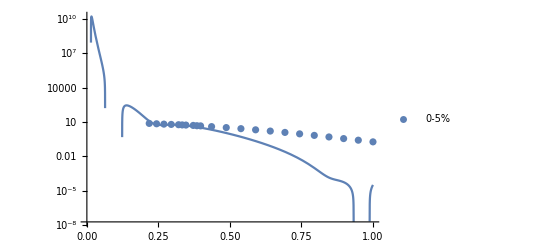

```mathematica
%57/.{k->0.45,q->0.4};
Show[LogPlot[%*10^5,{x,0,1}],data]
```

## Net proton distribution in n+A collision

```mathematica
GUDD[y1_,y2_,y3_]:=g(y1 )^β(y2 y3)^α DiracDelta[y1+y2+y3-1];
GU[y_]:=y^1.05 (38.556662 (1-1 y)^4.5-77.113324 (1-1 y)^2.75 );
GD[y_]:=y^1.75 (71.9047277 (1-1 y)^3.8-143.8094554(1.-1 y)^2.75 );
α=1.75;β=1.05;
(*∫_0^1 (∫_0^(1-y1) (∫_0^(1-y1-y2) y1^(n1-1)y2^(n2-1)y3^(n3-1)GUDD[y1,y2,y3]ⅆy3)ⅆy2)ⅆy1*)
GUDDm[n1_,n2_,n3_]:=(780.17132 Gamma[1.05+n1] Gamma[1.75+n2] Gamma[1.75+n3])/Gamma[4.55+n1+n2+n3]; 
GUDD1m[n1_,n2_,n3_]:=1/3^v Sum[(v!)/(v1!v2!(v-v1-v2)!)GUDDm[n1,n2,n3]Dm[n1,v1]Dm[n2,v2]Dm[n3,v-v1-v2],{v1,0,v},{v2,0,v-v1}];
GUD1m[m1_,m2_]:=GUDD1m[m1,1,m2];
GDD1m[m1_,m2_]:=GUDD1m[1,m1,m2];
N0=g^2 Beta[2β+2,2α+2β+4]Beta[2β+2,2α+2];
Fpm[n1_,n2_,n3_]:=2GUDD1m[n1,n2,n3]Vfm[v1,n1]Vum[v2,n2]Vfm[v3,n3]+GUDD1m[n2,n3,n1]Vum[v2,n1]Vum[v3,n2]Vum[v1,n3]+2GDD1m[n1,n2+n3-1]Vum[v2,n1]Wfum[v3,n2,n3]+2GDD1m[n3,n1+n2-1]Vfm[v2,n3]Wuum[v3,n1,n2]+2GUD1m[n1,n2+n3-1]Vfm[v1,n1]Wfum[v2,n2,n3]+2GUD1m[n3,n1+n2-1]Vum[v1,n3]Wuum[v2,n1,n2]+2GUD1m[n2+n3-1,n1]Wfum[v1,n2,n3]Vum[v2,n1]+2GUD1m[n1+n2-1,n3]Wffm[v1,n1,n2]Vfm[v2,n3];
Hp1m[n_]:=Sum[(n!)/(n1!n2!(n-n1-n2)!)Fpm[n1+β+3,n2+β+3,(n-n1-n2)+α+3],{n1,0,n},{n2,0,n-n1}];
Fpbarm[n1_,n2_,n3_]:=2GUDD1m[n1,n2,n3]Vfmbar[v1,n1]Vumbar[v2,n2]Vfmbar[v3,n3]+GUDD1m[n2,n3,n1]Vumbar[v2,n1]Vumbar[v3,n2]Vumbar[v1,n3]+2GDD1m[n1,n2+n3-1]Vumbar[v2,n1]Wfumbar[v3,n2,n3]+2GDD1m[n3,n1+n2-1]Vfmbar[v2,n3]Wuumbar[v3,n1,n2]+2GUD1m[n1,n2+n3-1]Vfmbar[v1,n1]Wfumbar[v2,n2,n3]+2GUD1m[n3,n1+n2-1]Vumbar[v1,n3]Wuumbar[v2,n1,n2]+2GUD1m[n2+n3-1,n1]Wfumbar[v1,n2,n3]Vumbar[v2,n1]+2GUD1m[n1+n2-1,n3]Wffmbar[v1,n1,n2]Vfmbar[v2,n3];
Hpbar1m[n_]:=Sum[(n!)/(n1!n2!(n-n1-n2)!)Fpbarm[n1+β+3,n2+β+3,(n-n1-n2)+α+3],{n1,0,n},{n2,0,n-n1}];
Hp[x_]:=g/N0 x^(-2β-α-4)H1p[x];
Hpbar[x_]:=g/N0 x^(-2β-α-4)H1pbar[x];
Hfromn[x_]:=Hp[x]-Hpbar[x];(*Hpp[x] should be calculated by Hp[x] and Hpbar[x] respectively, instead of Hpp1m[x]*)
```

```mathematica
Hfromn[x];
Export["Hxfromn.txt",Hfromn[x]];
```

## Net proton distribution in 79p&118n+A collision

```mathematica
SetDirectory[SystemDialogInput["Directory"]];
```

```mathematica
<<"Hx_vi=2.txt";
```

```mathematica
<<"Hxfromn_vi=2.txt";
```

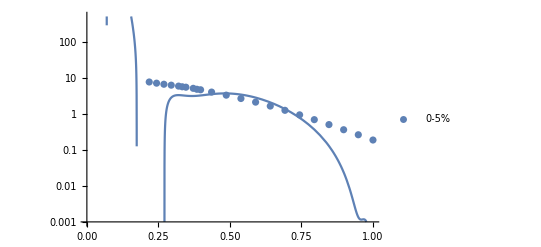

```mathematica
79*%85+118*%86/.{k->-0.5,q->0.37};
Show[LogPlot[%,{x,0,1}],data]
```

```mathematica
s[k_,q_]:=79*%172+118*%173
```

```mathematica
{#[[1]]/1.95,#[[2]]}&/@ListData["proton","0-5%"]
```

{{0.217949,7.6679},{0.24359,7.1124},{0.269231,6.6389},{0.294872,6.2556},{0.320513,5.892},{0.346154,5.4943},{0.371795,5.1139},{0.397436,4.6603},{0.333333,5.6473},{0.384615,4.8108},{0.435897,4.022},{0.487179,3.3034},{0.538462,2.6646},{0.589744,2.1118},{0.641026,1.6427},{0.692308,1.2511},{0.74359,0.9361},{0.794872,0.6884},{0.846154,0.502},{0.897436,0.3612},{0.948718,0.2618},{1.,0.187}}

```mathematica
79*%172+118*%173;
Table[%,{x,%219[[All,1]]}]
```

$Aborted[]

```mathematica
Assuming[k>0&&q>0,Minimize[(((79*%2+118*%3)/.x->0.435897435897436)-4.022)^2,{k,q}]]
```

{2.99475×10^-21,{k→-0.493856,q→-0.121491}}